2 ⅇ^(-0.05 t) Cos[t]

-0.1 ⅇ^(-0.05 t) Cos[t]-2 ⅇ^(-0.05 t) Sin[t]

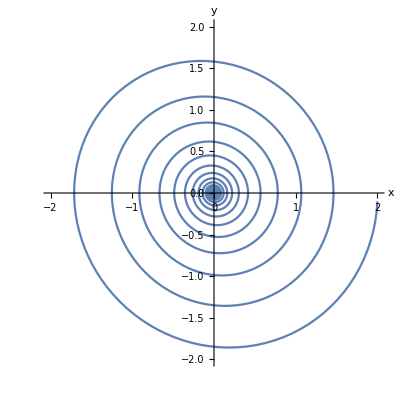

```mathematica
Remove["Global`*"]
x[t_]= 2*Cos[t]*Exp[-.05t]
v[t_] = -2*Sin[t]*Exp[-.05t]- 0.1 *Cos[t]*Exp[-.05t]

ParametricPlot[{x[t], v[t]}, {t, 0, 200}, PlotRange -> {{-2, 2},{-2,2}}, AxesLabel->{"x","y"}]
```